# Polymer Visualization and Statistical Analysis

## Random Polymers: A Polymer as a Random Walk

### The simplest model of polymer morphology is a sequence of uncorrelated bond lengths. This can be modeled with a random walk.

#### Uncorrelated Random Walk Model of a Polymer

We will fix the bond length to be equal to 2 and visualize the polymers as spheres of radius 1.

Here are two quick examples of visualizing such a random walk with 32 molecular units

```mathematica
steps = AngleVector[{2,#}]&/@RandomReal[{0,2π},32];
positions = Prepend[Accumulate[steps],{0,0}];
Graphics[

]
```

In 3 dimensions, we can use points on a sphere of radius 2 for the step directions

```mathematica
steps = RandomPoint[Sphere[{0,0,0},2],32];
positions = Prepend[Accumulate[steps],{0,0,0}];
Graphics3D[

]
```

#### Expected Length of an Uncorrelated Polymer as a Function of the Number of Units

We can use a Monte Carlo method to generate a set of random walks for a fixed number of units, an then compute the mean of the displacement from the origin of the walk.  Then we can repeat this for different numbers of units.

This function returns the net displacement of an uncorrelated random walk with step lengths of 1

```mathematica
Norm[
Total[ (*net displacement vector*)
RandomPoint[Sphere[],10] (*unit length steps*)
]
]
```

```mathematica
displacement[nUnits_, dimension_/;1<= dimension<= 3]:=
 Norm[
Total[ (*net displacement vector*)
Which[
dimension==1,RandomChoice[{-1,1}],
dimension==2,RandomPoint[Circle[],nUnits],
True,RandomPoint[Sphere[],nUnits]
]
]
]
```

Making sample sizes of 1000 for different numbers of units and computing their means and standard deviations.

```mathematica
displacementData = Table[{2^units,displacement[2^units, 3]},{units,10,18},1000];
(*computation takes about 30 seconds*)
```

```mathematica
meanDisplacements = Mean/@displacementData;
standardDeviationDisplacements = StandardDeviation/@displacementData;
```

```mathematica
Show[
ListPlot[displacementData,],ListLinePlot[MapThread[{#1,Around[#2,#3]}&,{First/@meanDisplacements,Last/@meanDisplacements,Last/@standardDeviationDisplacements}],]
]
```

Let’s see if we can discover the relation between the expected length and number of units

```mathematica
model = a (n)^power;
fit = FindFit[meanDisplacements,model,{a,power},n]
```

```mathematica
fitModel = model/.fit
```

The fit shows that the length increases as 
In our simulation, each If each bond had length = 1.  If the bond length were a, then the results would have been

George, if I had a way to insert “extra stuff, or footnote stuff, I would relate this to diffusion.

```mathematica
probabilityOfAtomPosition3D =Exp[-x^2/(4 diffCoeff t)]/((4 Pi  diffCoeff t )^(3/2))
```

normalized

```mathematica
Integrate[4 Pi x^2  probabilityOfAtomPosition3D,{x,0,Infinity}, Assumptions->diffCoeff> 0 && t> 0]
```

Mean displacement

```mathematica
Integrate[4 Pi x^3  probabilityOfAtomPosition3D,{x,-Infinity,Infinity}, Assumptions->diffCoeff> 0 && t> 0]
```

Mean squared displacement

```mathematica
msqd =Integrate[4 Pi x^4  probabilityOfAtomPosition3D,{x,-Infinity,Infinity}, Assumptions->diffCoeff> 0 && t> 0]
```

```mathematica
Sqrt[msqd/.diffCoeff->1/6]
```

????
 The coefficient seems closer to 1 than .  Does the diffusion equation approximation must over estimate the RMS displacement.  This is reasonable as the derivation produces particles that travel infinitely fast, so there is something in Stirling’s appx that maybe is accounting for this error
 ???

End Footnote

```mathematica
Show[
ListPlot[meanDisplacements,
],
Plot[fitModel,{n,1,10^7}]]
```

Thus, we demonstrate that the expected length polymer with uncorrelated bond direction increases as the square-root of the number of molecular units.

## “Models of Stiff Polymers” Creating a Polymer with Correlations

Some polymers may be less “floppy”: there will be a smaller range of “bending angle” at each molecular unit.
This would create direction correlations in the polymer chain. 

We can model this by creating a correlation in the steps by selecting new directions within a given angle of the previous angle.

In two dimensions, this would be an arc of a circle centered on the previous direction.  In three dimensions, this would be points withing a given solid angle on a sphere.

Two dimensions is  straightforward.  The next direction is chosen from a uniform distribution of angles around the last direction  Δϕ < θ < Δϕ.   AnglePath does exactly this:

```mathematica
Manipulate[
With[{steps = AnglePath[{2,#}&/@RandomReal[{-range/2,range/2},12]]},
Graphics[

]
],
{range,0,2Pi}
]
```

For three dimensions, we need an algorithm to produce random points from a uniform spatial distribution over a spherical cap.

We begin by constructing a formula to find a point on a sphere within a cone aligned with {1,0,0} with a given solid  angle:

```mathematica
Manipulate[
Graphics3D[
{Opacity[0.5], Blue,Sphere[],Green,Cone[{ Sign[Tan[ ϕ/4]]{0,0,1},{0,0,0}},Abs@Tan[ ϕ/4]],
Red,Torus[{0,0,Cos[ϕ/4]},{Sin[ϕ/4],Sin[ϕ/4]+.05}]
},Axes->True,AxesLabel->{"Z","Y","X"}],
{ϕ,0.1,4Pi}
]
```

The red circle above is  intersection of the cone and the sphere. The circle is located at a height z=Cos[ϕ/4] and has a radius r = Sin[ϕ/4].
The probability density of a random point having a radius r is proportional to the circumference of the circle.  The normalized distribution of finding an angle less than α is proportional to:

```mathematica
Integrate[Sin[ϕ/4],{ϕ,0,α}]
```

Normalizing this cumulative probability distribution:

```mathematica
probα=Integrate[Sin[ϕ/4],{ϕ,0,α}]/(8 Sin[αMax/8]^2)
```

Letting a value p be chosen from a uniform 0 < p < 1, then the probability distribution for 0 < α < α_max is

```mathematica
Solve[probα==p,α]
```

This probability method  is employed in another notebook to compute the Partition function of a polymer.  The solid angle scales how many configurations are available and we can associate an energy with the amount of bending.

We can use this result to find a random radius of the circle and its height.  Letting {x,y} be chosen from a uniform distribution on that circle:

```mathematica
randomPointSphericalCap[αMax_]:=Module[{phi =8 ArcSin[Sqrt[RandomReal[{0,1}]]Sin[αMax/8]],r},
r = Sin[phi/4];
Flatten[{Cos[phi/4],r AngleVector[RandomReal[{0,2Pi}]]}]
]
```

```mathematica
randomPointSphericalCap[αMax_,n_]:=Module[{phi =8 ArcSin[Sqrt[RandomReal[{0,1},n]]Sin[αMax/8]],r},
r = Sin[phi/4];
MapThread[
Flatten[{#3,#1 AngleVector[#2]}]&,{r,RandomReal[{0,2Pi},n],Cos[phi/4]}]
]
```

Example

```mathematica
Manipulate[
Graphics3D[Point[randomPointSphericalCap[α,n]]],
{α,0.01,4Pi},
{n,10,2000}
]
```

It will be useful to have a version of this function that returns the rotation matrices the moves a point from {0,0,1} to a random point in the cap of solid angle α_max.

```mathematica
randomPointSphericalCapRotationMatrix[αMax_,n_]:=
Map[
RotationMatrix[{{1,0,0},#}]&,
randomPointSphericalCap[αMax,n]
]
```

```mathematica
MatrixForm/@randomPointSphericalCapRotationMatrix[Pi/6,3]
```

{(0.999167 | 0.0287137 | -0.0289994
-0.0287137 | 0.999588 | 0.000416513
0.0289994 | 0.000416513 | 0.999579),(0.997698 | -0.0255948 | 0.0628053
0.0255948 | 0.999672 | 0.00080467
-0.0628053 | 0.00080467 | 0.998025),(0.998102 | -0.0309314 | 0.0532519
0.0309314 | 0.999521 | 0.000824361
-0.0532519 | 0.000824361 | 0.998581)}

To create this correlated walk, we accumulate vectors that are incrementally rotated.
AnglePath3D does this.
To illustrate, suppose we have a sequence of 20 small rotations around the y-axis:

```mathematica
rotations = Table[RotationMatrix[{{0,0,1},{.1,0,1}}],20];

Graphics3D[Sphere[#,1/2]&/@AnglePath3D[rotations]]
```

-Graphics3D-

```mathematica
Last[AnglePath3D[rotations]]
```

{8.43804,0.,-14.5923}

This is equivalent to a “Folding” a dot-product over the list of rotations:  and then accumulating the vectors in the list:

```mathematica
accumulatedRotations = FoldList[#1.#2&,rotations];
```

```mathematica
steps = #.{1,0,0}&/@accumulatedRotations
```

{{0.995037,0.,-0.0995037},{0.980198,0.,-0.19802},{0.95563,0.,-0.29457},{0.921576,0.,-0.388197},{0.878376,0.,-0.477971},{0.826457,0.,-0.563001},{0.766334,0.,-0.642442},{0.698606,0.,-0.715507},{0.623943,0.,-0.78147},{0.543088,0.,-0.839676},{0.456841,0.,-0.889548},{0.366061,0.,-0.930591},{0.271647,0.,-0.962397},{0.174537,0.,-0.984651},{0.0756941,0.,-0.997131},{-0.0238998,0.,-0.999714},{-0.123257,0.,-0.992375},{-0.22139,0.,-0.975185},{-0.317326,0.,-0.948317},{-0.410112,0.,-0.912035}}

The only difference is that AngleVector3D prepends a point at {0,0,0}.  This will not be important for our purposes.

```mathematica
Graphics3D[{Opacity[0.2],Blue,Sphere[#,1/2]&/@AnglePath3D[rotations],Red,Opacity[1],Sphere[#,.4]&/@Accumulate[steps]}]
```

-Graphics3D-

```mathematica
Length[Accumulate[steps]]
Length[AnglePath3D[rotations]]
```

The advantage of the Fold method is that:
1) It is much faster:

We can demonstrate that it is faster below for 50000 rotations:

```mathematica
(*rotations = randomPointSphericalCapRotationMatrix[Pi,200];
rotations = ConstantArray[RotationMatrix[{{0,0,1},{1,1,0}}],1000];*)
```

```mathematica
rotations = randomPointSphericalCapRotationMatrix[Pi/4,50000];
```

For AnglePath

In addition to the computation time, we will keep track of the final position to be sure the methods are consistent:

```mathematica
{timingAP,lastPosAP} =RepeatedTiming[Last[pathAP =AnglePath3D[rotations]]]
```

{0.059406,{2034.76,410.247,-1602.42}}

For the fold method:

```mathematica
{timingFP1,lastPosFP1} =RepeatedTiming[Last@Accumulate[pathFP1=(#.{1,0,0})&/@FoldList[Dot[#1,#2]&,rotations]]]
```

{0.015451,{2034.76,410.247,-1602.42}}

Moreover, the Dot product above    picks out the first column of 
Instead of the Dot product, we can grab the column:

```mathematica
{timingFP2,lastPosFP2} =RepeatedTiming[Last@Accumulate[pathFP2=(#[[All,1]])&/@FoldList[Dot[#1,#2]&,rotations]]]
```

{0.0171157,{2034.76,410.247,-1602.42}}

Even better, we can pick out all of the first columns at once:

```mathematica
{timingFP3,lastPosFP3} =RepeatedTiming[Last@Accumulate[pathFP3=(FoldList[Dot[#1,#2]&,rotations][[All,All,1]])]]
```

{0.0113388,{2034.76,410.247,-1602.42}}

We get a speed up of about 5×

```mathematica
timingAP/timingFP3
```

5.31376

If we only need the final point:

```mathematica
{timingFP4,lastPosFP4} =RepeatedTiming[Total[(FoldList[Dot[#1,#2]&,rotations][[All,All,1]])]]
```

{0.0110081,{2034.76,410.247,-1602.42}}

```mathematica
orit
```

We’ve established an algorithm to embed into functions:

```mathematica
randomCorrelatedWalk[units_, α_]:= 
With[{rotations = 
randomPointSphericalCapRotationMatrix[α,units]},
Accumulate[(FoldList[Dot[#1,#2]&,rotations][[All,All,1]])]
]
```

```mathematica
randomCorrelatedDisplacement[units_, α_]:= 
With[{rotations = 
randomPointSphericalCapRotationMatrix[α,units]},
Norm[Total[(FoldList[Dot[#1,#2]&,rotations][[All,All,1]])]]
]
```

Visualizing random instances of correlated paths:

```mathematica
Manipulate[
With[{path=randomCorrelatedWalk[units, α]},
Graphics3D[
MapThread[{Hue[#2],Sphere[#1,0.5]}&,{path,0.6 Rescale[Range[Length[path]]]}]
]
],
{α,0.1,4 Pi},
{units,5,500,1}
]
```

As before, we can do Monte Carlo experiments to find the expected length of a correlated polymer.
We will do repeated experiments for 24 solid angles from {(π,)/6 π/3,(3π)/16,…,4π}.

As we will see below, the computation is time-consuming—which is why we spent some effort above making things faster.

To get a sense of how long each experiment will take:

```mathematica
timingData =Table[{2^units,AbsoluteTiming[randomCorrelatedDisplacement[2^units, Pi/2]]}//Flatten,{units,2,18}]
```

{{4,0.001021,3.89234},{8,0.000763,7.47885},{16,0.001393,14.0693},{32,0.002696,25.2652},{64,0.005276,53.4876},{128,0.011154,62.9944},{256,0.020831,108.893},{512,0.040674,76.6149},{1024,0.082024,143.453},{2048,0.163232,349.248},{4096,0.324992,299.338},{8192,0.661737,269.29},{16384,1.29981,947.064},{32768,2.59217,1961.44},{65536,5.19872,1533.44},{131072,10.5652,1278.79},{262144,21.0918,3560.66}}

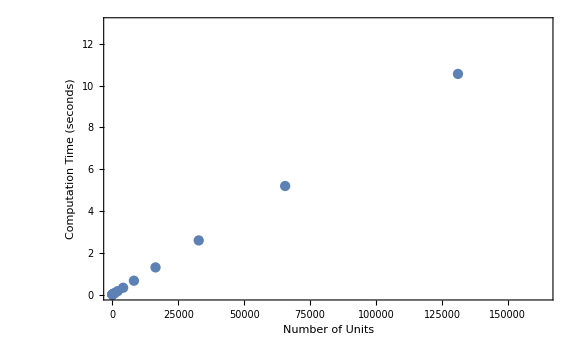

```mathematica
ListPlot[timingData[[All,1;;2]], Frame->True, FrameLabel-> {"Number of Units","Computation Time (seconds)"},ImageSize->Large, BaseStyle->18]
```

The total time we need to do 1 experiment for up to 262144 units is about one minute:

```mathematica
totalTime= Total[timingData[[All,2]]]
```

42.0635

If we do all the angles in parallel (i.e., ParallelTable) it takes about 4 minutes (8 CPUs)

```mathematica
AbsoluteTiming[result=
ParallelTable[
Table[α->{2^units,randomCorrelatedDisplacement[2^units, Pi/2]},{units,2,18}],
{α,Pi/6,4Pi,Pi/6}
];
]
```

{211.18,Null}

Supposing we had enough patience to wait  1 hour, we could only do 15 repeated experiments.  This is likely insufficient for good statistics.

Another approach would be to do a single experiment for a large number of units, and then use the data from smaller subsequences of that data.   This would produce correlations in the data, so it is not ideal.

To do a single experiment in parallel, this takes about 2 minutes:

```mathematica
AbsoluteTiming[
result =ParallelTable[
<|α->With[{singleWalk =randomCorrelatedWalk[2^18, α]},
Table[<|2^n-> Norm[singleWalk[[2^n]]]|>,{n,2,18}]
]|>,
{α,Pi/6,4Pi,Pi/6}
]
]
```

{110.173,{<|π/6→{<|4→3.94392|>,<|8→7.67622|>,<|16→15.1419|>,<|32→28.1815|>,<|64→36.8966|>,<|128→54.5418|>,<|256→139.14|>,<|512→125.458|>,<|1024→340.795|>,<|2048→562.377|>,<|4096→660.444|>,<|8192→675.753|>,<|16384→520.803|>,<|32768→321.833|>,<|65536→835.545|>,<|131072→1260.43|>,<|262144→3323.08|>}|>,<|π/3→{<|4→3.90455|>,<|8→7.74188|>,<|16→14.4547|>,<|32→28.1311|>,<|64→41.719|>,<|128→81.1634|>,<|256→93.3609|>,<|512→90.892|>,<|1024→168.505|>,<|2048→233.345|>,<|4096→368.95|>,<|8192→129.15|>,<|16384→302.348|>,<|32768→618.67|>,<|65536→2080.47|>,<|131072→1986.16|>,<|262144→1808.87|>}|>,<|π/2→{<|4→3.90303|>,<|8→7.3869|>,<|16→14.8254|>,<|32→26.0202|>,<|64→47.8733|>,<|128→89.3735|>,<|256→144.39|>,<|512→144.347|>,<|1024→199.788|>,<|2048→365.225|>,<|4096→530.557|>,<|8192→566.743|>,<|16384→682.722|>,<|32768→402.371|>,<|65536→477.64|>,<|131072→795.984|>,<|262144→3093.78|>}|>,<|(2 π)/3→{<|4→3.83939|>,<|8→7.20191|>,<|16→13.5692|>,<|32→26.011|>,<|64→49.1932|>,<|128→82.0586|>,<|256→97.2319|>,<|512→86.923|>,<|1024→133.453|>,<|2048→233.371|>,<|4096→342.596|>,<|8192→623.488|>,<|16384→850.426|>,<|32768→212.29|>,<|65536→1276.78|>,<|131072→680.155|>,<|262144→1530.84|>}|>,<|(5 π)/6→{<|4→3.91692|>,<|8→7.69101|>,<|16→14.6908|>,<|32→23.5409|>,<|64→43.162|>,<|128→47.0942|>,<|256→86.0621|>,<|512→229.198|>,<|1024→304.808|>,<|2048→404.707|>,<|4096→471.677|>,<|8192→501.158|>,<|16384→698.778|>,<|32768→1523.21|>,<|65536→1834.18|>,<|131072→2777.2|>,<|262144→4043.63|>}|>,<|π→{<|4→3.93472|>,<|8→7.74702|>,<|16→14.6738|>,<|32→28.0787|>,<|64→47.1611|>,<|128→73.436|>,<|256→136.479|>,<|512→58.8254|>,<|1024→147.963|>,<|2048→241.525|>,<|4096→481.658|>,<|8192→524.842|>,<|16384→361.876|>,<|32768→934.051|>,<|65536→1827.42|>,<|131072→3617.58|>,<|262144→4503.43|>}|>,<|(7 π)/6→{<|4→3.95814|>,<|8→7.6226|>,<|16→14.3438|>,<|32→26.3146|>,<|64→23.7029|>,<|128→56.3561|>,<|256→107.911|>,<|512→72.2326|>,<|1024→191.655|>,<|2048→489.585|>,<|4096→597.278|>,<|8192→1199.35|>,<|16384→1459.85|>,<|32768→1956.05|>,<|65536→1552.03|>,<|131072→3326.72|>,<|262144→4818.31|>}|>,<|(4 π)/3→{<|4→3.90058|>,<|8→7.84087|>,<|16→14.6953|>,<|32→28.5011|>,<|64→47.1386|>,<|128→91.2233|>,<|256→96.1198|>,<|512→159.496|>,<|1024→316.225|>,<|2048→632.803|>,<|4096→844.628|>,<|8192→1204.63|>,<|16384→1255.05|>,<|32768→1917.44|>,<|65536→2100.05|>,<|131072→3512.11|>,<|262144→5350.42|>}|>,<|(3 π)/2→{<|4→3.84027|>,<|8→7.67595|>,<|16→14.5989|>,<|32→27.6207|>,<|64→56.673|>,<|128→102.278|>,<|256→120.947|>,<|512→171.686|>,<|1024→263.546|>,<|2048→451.536|>,<|4096→533.175|>,<|8192→706.711|>,<|16384→798.608|>,<|32768→667.693|>,<|65536→1318.03|>,<|131072→1056.79|>,<|262144→2792.95|>}|>,<|(5 π)/3→{<|4→3.81026|>,<|8→7.67709|>,<|16→14.005|>,<|32→26.5985|>,<|64→24.1926|>,<|128→49.1801|>,<|256→145.296|>,<|512→132.727|>,<|1024→214.083|>,<|2048→195.27|>,<|4096→339.157|>,<|8192→673.008|>,<|16384→495.497|>,<|32768→1707.72|>,<|65536→1801.2|>,<|131072→2541.74|>,<|262144→5117.26|>}|>,<|(11 π)/6→{<|4→3.73589|>,<|8→7.40179|>,<|16→14.3475|>,<|32→29.3967|>,<|64→42.7252|>,<|128→78.2727|>,<|256→111.574|>,<|512→175.859|>,<|1024→194.439|>,<|2048→299.026|>,<|4096→479.641|>,<|8192→931.85|>,<|16384→590.888|>,<|32768→651.841|>,<|65536→1311.26|>,<|131072→1028.23|>,<|262144→4893.83|>}|>,<|2 π→{<|4→3.89507|>,<|8→7.44485|>,<|16→13.1746|>,<|32→27.9833|>,<|64→57.4061|>,<|128→103.373|>,<|256→99.5033|>,<|512→152.02|>,<|1024→233.151|>,<|2048→420.42|>,<|4096→516.402|>,<|8192→444.4|>,<|16384→1177.76|>,<|32768→777.591|>,<|65536→1532.84|>,<|131072→2104.42|>,<|262144→1170.51|>}|>,<|(13 π)/6→{<|4→3.93393|>,<|8→7.50482|>,<|16→14.2888|>,<|32→28.5796|>,<|64→48.5238|>,<|128→26.1368|>,<|256→28.627|>,<|512→71.2983|>,<|1024→109.922|>,<|2048→140.889|>,<|4096→314.78|>,<|8192→187.004|>,<|16384→506.969|>,<|32768→1233.64|>,<|65536→843.433|>,<|131072→1311.93|>,<|262144→2285.21|>}|>,<|(7 π)/3→{<|4→3.90431|>,<|8→7.47608|>,<|16→14.5479|>,<|32→26.5691|>,<|64→48.4917|>,<|128→75.1132|>,<|256→10.7051|>,<|512→92.9069|>,<|1024→165.378|>,<|2048→232.506|>,<|4096→364.101|>,<|8192→456.217|>,<|16384→551.687|>,<|32768→553.849|>,<|65536→1157.31|>,<|131072→1329.33|>,<|262144→2074.7|>}|>,<|(5 π)/2→{<|4→3.90484|>,<|8→7.54603|>,<|16→15.1529|>,<|32→29.0385|>,<|64→46.6446|>,<|128→86.0955|>,<|256→95.7236|>,<|512→97.4819|>,<|1024→257.907|>,<|2048→232.132|>,<|4096→527.891|>,<|8192→557.307|>,<|16384→554.892|>,<|32768→1314.93|>,<|65536→1483.24|>,<|131072→866.306|>,<|262144→1131.9|>}|>,<|(8 π)/3→{<|4→3.93376|>,<|8→7.51245|>,<|16→14.1124|>,<|32→27.332|>,<|64→53.4019|>,<|128→87.5037|>,<|256→91.5285|>,<|512→74.9723|>,<|1024→79.7121|>,<|2048→414.961|>,<|4096→649.777|>,<|8192→433.322|>,<|16384→817.817|>,<|32768→1989.17|>,<|65536→2589.92|>,<|131072→2976.3|>,<|262144→4038.94|>}|>,<|(17 π)/6→{<|4→3.85166|>,<|8→7.50217|>,<|16→10.4042|>,<|32→20.5279|>,<|64→39.9278|>,<|128→70.3443|>,<|256→115.243|>,<|512→225.109|>,<|1024→321.831|>,<|2048→42.6729|>,<|4096→320.8|>,<|8192→701.346|>,<|16384→1023.91|>,<|32768→1365.41|>,<|65536→1761.44|>,<|131072→2022.99|>,<|262144→5932.87|>}|>,<|3 π→{<|4→3.84218|>,<|8→7.74845|>,<|16→15.2834|>,<|32→27.8584|>,<|64→53.9775|>,<|128→88.7604|>,<|256→100.85|>,<|512→88.0822|>,<|1024→126.101|>,<|2048→291.63|>,<|4096→118.468|>,<|8192→718.022|>,<|16384→846.636|>,<|32768→1348.33|>,<|65536→1065.95|>,<|131072→1555.88|>,<|262144→2241.52|>}|>,<|(19 π)/6→{<|4→3.961|>,<|8→7.63495|>,<|16→14.1723|>,<|32→26.6578|>,<|64→30.5455|>,<|128→71.7316|>,<|256→106.682|>,<|512→122.285|>,<|1024→109.376|>,<|2048→92.911|>,<|4096→416.166|>,<|8192→559.46|>,<|16384→579.882|>,<|32768→831.875|>,<|65536→1657.65|>,<|131072→3156.9|>,<|262144→2921.86|>}|>,<|(10 π)/3→{<|4→3.96479|>,<|8→7.67333|>,<|16→13.9929|>,<|32→23.9336|>,<|64→41.3865|>,<|128→70.0152|>,<|256→120.92|>,<|512→122.51|>,<|1024→129.083|>,<|2048→287.333|>,<|4096→378.233|>,<|8192→415.268|>,<|16384→713.494|>,<|32768→977.433|>,<|65536→579.671|>,<|131072→1653.54|>,<|262144→3709.72|>}|>,<|(7 π)/2→{<|4→3.79333|>,<|8→7.52566|>,<|16→15.0235|>,<|32→29.188|>,<|64→53.6023|>,<|128→98.7745|>,<|256→93.1752|>,<|512→125.378|>,<|1024→226.689|>,<|2048→226.265|>,<|4096→176.615|>,<|8192→318.835|>,<|16384→803.306|>,<|32768→1395.45|>,<|65536→2310.94|>,<|131072→2305.1|>,<|262144→7327.77|>}|>,<|(11 π)/3→{<|4→3.92794|>,<|8→7.75246|>,<|16→15.2044|>,<|32→28.5809|>,<|64→56.5818|>,<|128→58.58|>,<|256→112.268|>,<|512→116.241|>,<|1024→357.346|>,<|2048→342.472|>,<|4096→149.262|>,<|8192→661.189|>,<|16384→756.395|>,<|32768→1344.94|>,<|65536→1152.39|>,<|131072→1708.01|>,<|262144→3052.81|>}|>,<|(23 π)/6→{<|4→3.91681|>,<|8→7.53022|>,<|16→13.3571|>,<|32→26.8947|>,<|64→54.9542|>,<|128→66.0283|>,<|256→97.0869|>,<|512→82.8114|>,<|1024→176.625|>,<|2048→329.27|>,<|4096→385.758|>,<|8192→872.453|>,<|16384→1512.69|>,<|32768→2403.33|>,<|65536→2378.59|>,<|131072→4167.03|>,<|262144→3453.11|>}|>,<|4 π→{<|4→3.93314|>,<|8→7.47506|>,<|16→14.4066|>,<|32→29.6302|>,<|64→34.5791|>,<|128→54.7173|>,<|256→156.015|>,<|512→134.751|>,<|1024→131.4|>,<|2048→222.787|>,<|4096→586.495|>,<|8192→366.31|>,<|16384→440.137|>,<|32768→746.601|>,<|65536→1014.|>,<|131072→4303.24|>,<|262144→6132.93|>}|>}}

So, our patience limit of 1 hour would permit 30 Monte Carlo repetitions.
Can you  find something interesting or fun (optimally both) to do for 6 minutes and let it run?

```mathematica
AbsoluteTiming[
With[{monteCarloExperiments = 3, nExponent= 18},
correlatedRandomWalkData =
Association[
ParallelTable[
<|α->
With[{walkExperiments =
Table[randomCorrelatedWalk[2^nExponent, α],monteCarloExperiments]
},
Table[
<|2^n->
<|"Monte Carlo Experiments"->monteCarloExperiments,
"Mean"->Mean[Norm/@walkExperiments[[All,2^n]]],"Standard Deviation"-> StandardDeviation[Norm/@walkExperiments[[All,2^n]]]|>|>,{n,2,nExponent}]
]|>,
{α,Pi/6,4Pi,Pi/6}
]
];
]
]
```

```mathematica
AbsoluteTiming[
With[{monteCarloExperiments = 300, nExponent= 18},
correlatedRandomWalkData =
Association[
ParallelTable[
<|α->
With[{walkExperiments =
Table[randomCorrelatedWalk[2^nExponent, α],monteCarloExperiments]
},
Table[
<|2^n->
<|"Monte Carlo Experiments"->monteCarloExperiments,
"Mean"->Mean[Norm/@walkExperiments[[All,2^n]]],"Standard Deviation"-> StandardDeviation[Norm/@walkExperiments[[All,2^n]]]|>|>,{n,2,nExponent}]
]|>,
{α,Pi/6,4Pi,Pi/6}
]
];
]
]
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"correlatedRandomWalkData.mx"}],correlatedRandomWalkData];
```

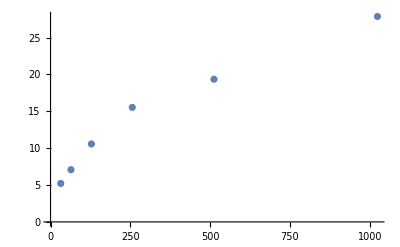

```mathematica
ListPlot[Mean/@data[ 4Pi]]
```

```mathematica
{#[[1,1]],StandardDeviation/@#[[All,2]]}&/@{data[Pi/6],data[Pi]}
```

```mathematica
meanDisplacements =<|(#-> Mean/@data[#])&/@Range[Pi/6,4Pi,Pi/6]|>;
standardDeviationDisplacements =<|(#-> StandardDeviation/@data[#])&/@Range[Pi/6,4Pi,Pi/6]|>;
```

```mathematica
{First/@meanDisplacements,Last/@meanDisplacements,Last/@standardDeviationDisplacements}
```

```mathematica
standardDeviationDisplacements[Pi/6]
```

```mathematica
standardDeviationDisplacements[Pi/6]
```

```mathematica
With[{α=Pi/6},ListLinePlot[MapThread[{#1,Around[#2,#3]}&,{First/@meanDisplacements[α],Last/@meanDisplacements[α],Last/@standardDeviationDisplacements[α]}],PlotMarkers->{"◆",25},PlotStyle->{Directive[Black,PointSize[0.03],Thickness[0.005]]}]
]
```

```mathematica
Manipulate[
Show[
ListPlot[data[α],Frame->True,FrameLabel->{"Number of Molecular Units","Length"},ImageSize->Large,BaseStyle->{FontSize->18},PlotLabel->"Length of 1000 Polymers with Bond Rigidity\nfor Variable Molecular Weight",PlotStyle->{Directive[Opacity[0.2],PointSize[0.02]]},PlotRange->{All,{-1,20}}],ListLinePlot[MapThread[{#1,Around[#2,#3]}&,{First/@meanDisplacements[α],Last/@meanDisplacements[α],Last/@standardDeviationDisplacements[α]}],PlotMarkers->{"◆",25},PlotStyle->{Directive[Black,PointSize[0.03],Thickness[0.005]]}]
],
{α,Range[Pi/6,4Pi,Pi/6]}
]
```

Finding the power law fit:

```mathematica
model
```

```mathematica
fit=FindFit[Flatten[data[#],1],model,{a,power},n]&/@Range[Pi/6,4Pi,Pi/6];
model/.fit
```

Finding the power law as a function of the polymer rigidity

```mathematica
rigidityFit[rigidity_,simulations_?IntegerQ]:=
 Block[{
data=Table[{2^units,Norm[displacement[2^units,rigidity °,1]]},{units,1,10},simulations],
a,n,power
},
Flatten[{rigidity,{a,power}/.FindFit[Flatten[data,1],a n^power,{a,power},n]}]
]
```

```mathematica
results =rigidityFit[#,500]&/@{5,10,15,30,45,90,180};
```

```mathematica
ListLinePlot[results[[All,{1,3}]], ]
```

#### The power law dependence on rigidity can be computed by the correlation method described in Section 7.2 of Kinetics of Materials by Baluffi, Allen, Carter